# Finite Difference Methods

## Fully implicit method

Backward-difference (fully implicit) method for solving Fick’s Second Law for a potential step to the limiting current region for the reaction O+e⇌R.

Version 1.30
copyright © 2002-Year Michael Honeychurch

## Mathematica Preliminaries

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"],Clear["Global`*"]];
```

```mathematica
Off[General::"spell"];
Off[General::"spell1"];
```

```mathematica
SetOptions[ListPlot3D,
AspectRatio-> 1,
AxesLabel->{
Style["k",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
Style["j",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
Style["c  ",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Plain,FontWeight-> Bold]},
ImageSize->400,
ViewPoint->{2,-.5,1},
Mesh->False,
PlotRange->All];
```

```mathematica
SetOptions[ListPlot,
Axes-> False,
Frame-> True,
FrameLabel-> {
Style["k",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
Style["z",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
None,
None}, 
FormatType-> TraditionalForm,
GridLines->None,
ImageSize->400,
Joined-> False,
PlotRegion-> {{0,1},{0.1,0.9}},
PlotLabel-> None,
PlotStyle->{Black,AbsoluteThickness[1]},
Prolog-> {Green,AbsolutePointSize[4.5]}];
```

```mathematica
closeFrames:=With[{nb=EvaluationNotebook[]},SelectionMove[nb,All,GeneratedCell];
FrontEndTokenExecute["CellGroup"];
FrontEndExecute[FrontEndToken["OpenCloseGroup"]];
SelectionMove[nb,All,CellGroup];
FrontEndExecute[FrontEnd`SelectionAnimate[nb,5]];]
```

```mathematica
$Line=0;
```

## Make Diagonals and Matrix

```mathematica
Clear[makeDiagonals];

makeDiagonals[m_Integer,d_]:=
	Module[{x,y,z},
		x=Table[-d,{m-3}];
		z=Table[-d,{m-3}];
		y=Table[1.+2.*d,{m-2}];
{x,y,z}]
```

```mathematica
{x,y,z}=makeDiagonals[7,𝔻]
```

{{-𝔻,-𝔻,-𝔻,-𝔻},{1.+2. 𝔻,1.+2. 𝔻,1.+2. 𝔻,1.+2. 𝔻,1.+2. 𝔻},{-𝔻,-𝔻,-𝔻,-𝔻}}

```mathematica
SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},5]
```

SparseArray[…]

```mathematica
Clear[makeMatrix];
makeMatrix[x_,y_,z_]:=Module[{n=Length[y]},
SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},n]
]
```

```mathematica
MatrixForm[makeMatrix[x,y,z]]
```

(1.+2. 𝔻 | -𝔻 | 0 | 0 | 0
-𝔻 | 1.+2. 𝔻 | -𝔻 | 0 | 0
0 | -𝔻 | 1.+2. 𝔻 | -𝔻 | 0
0 | 0 | -𝔻 | 1.+2. 𝔻 | -𝔻
0 | 0 | 0 | -𝔻 | 1.+2. 𝔻)

## Set Up Solution

#### LinearSolve Solution

```mathematica
Clear[implicitSolve];

implicitSolve[m_Integer,n_Integer,d_]:=Module[{x,y,z,len,mat,initial,solveNext},
{x,y,z}=makeDiagonals[m,d];
len=Length[y];
mat=SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},len];
initial=ConstantArray[1.,{m}];
solveNext:=Module[{b},
b=#⟦2;;-2⟧;
b[[-1]]=b[[-1]]+d;
Flatten[{0.,LinearSolve[mat,b],1.}]]&;

NestList[solveNext,initial,n-1]
]
```

## Set Parameter Values

```mathematica
Clear[𝒟,time,n,m,Δt,𝔻];

𝒟=10.^-5.;
time=0.1;
n=400;
𝔻=0.5;
m=Ceiling[6*√(𝔻*(n-1))];
Δt=time/(n-1)//N;
```

## Solve

```mathematica
Clear[c];

Timing[
c=implicitSolve[m,n,𝔻];
Rest[c];
]
```

{0.041746,Null}

#### Comparison with analytical result

```mathematica
With[{p=60(*enter a time increment*),Δx=√((𝒟*Δt)/𝔻)},
Table[Erf[(j*Δx)/(2*Sqrt[𝒟*Δt*p])]/c⟦p,j+1⟧,{j,2,m-1}]
]
```

{0.985132,0.985781,0.986652,0.987707,0.988905,0.990197,0.991534,0.992869,0.994155,0.995354,0.996438,0.997383,0.99818,0.998826,0.999329,0.999702,0.999962,1.00013,1.00022,1.00026,1.00027,1.00025,1.00022,1.00018,1.00015,1.00011,1.00009,1.00006,1.00005,1.00003,1.00002,1.00001,1.00001,1.00001,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

## Plot current v. Time

### Plot current v. time

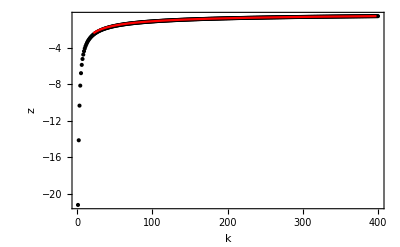

```mathematica
Clear[i,z];

i=Map[((-4*#⟦2⟧+#⟦3⟧)*0.5*√(𝔻*(n-1)))&,c];

z=Table[-1/Sqrt[Pi*(k-1)/(n-1)],{k,2,n-1}];

Show[ListPlot[i],ListPlot[z,Joined->True,PlotStyle->Red],
PlotRange-> {{0, n}, {0, -3}}]
```

### Animate current v. time plot

```mathematica
Animate[
ListPlot[Table[-c⟦k,2⟧*√(𝔻*(n-1)),{k,2,x}],PlotRange-> {{0, n}, {0, -3}}],
 {x, 2, n-1, 4}]
```

## Plot concentration profiles

```mathematica
ListPlot3D[Transpose@c]
```

-Graphics3D-

## Animation of Concentration Profile

This calculation can be animated to see how the concentration profile changes with time.

```mathematica
Animate[ListPlot3D[Transpose[Take[c,x]],PlotRange->{{1,n-1},{1,m},{0,1}}], {x, 1,n-1, 10}]
```